```mathematica
a={1,2,4,8};
p[x_,a_]:=Boole[Abs[x]<=a]/(2a)
b=10;
```

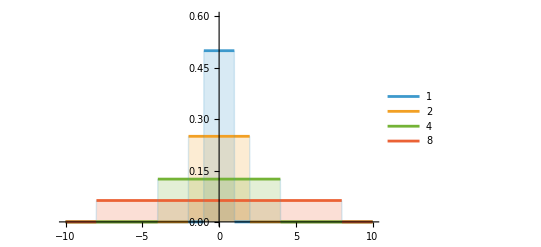

```mathematica
Plot[Evaluate[Table[p[x,c],{c,a}]],
{x,-b,b},
Filling->Bottom,
PlotLegends->a,
PlotRange->{Full,{0,1/(2*a[[1]])+0.1}}]
```

```mathematica
p1[x_]:=Boole[Abs[x]<=4]*0.25 (*U[0,4*)
p2[x_]:= 0.5*Exp[-0.5*x]     (*exp(1/2)*)
p3[x_]:=PDF[GammaDistribution[1/2, 2], x]
```

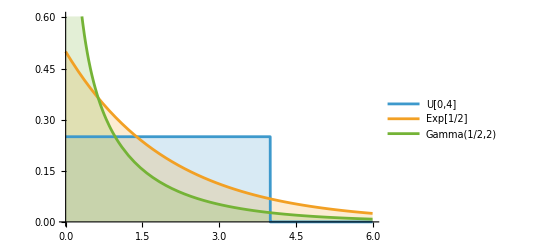

```mathematica
Plot[{p1[x],p2[x],p3[x]},{x,0,6},
Filling->Bottom,
PlotLegends->{"U[0,4]", "Exp[1/2]", "Gamma(1/2,2)"}]
```